# Sample Option Example

This example reuses Tutorial part 1. At the end we show how to modify the “Sample” method options

## Unmodified beginning of the Tutorial 1

```mathematica
<< CmdStan`
```

```mathematica
SetDirectory[$TemporaryDirectory]
```

/tmp

```mathematica
stanCode="data
{
  int<lower = 0> N;
  vector[N] x;
  vector[N] y;
}
parameters
{
  real alpha;
  real beta;
  real<lower = 0> sigma;
}
model {
  y ~normal(alpha + beta * x, sigma);
}";
```

```mathematica
stanExeFile = CompileStanCode[stanCodeFile,StanVerbose->False]
```

CompileStanCode[stanCodeFile,StanVerbose→False]

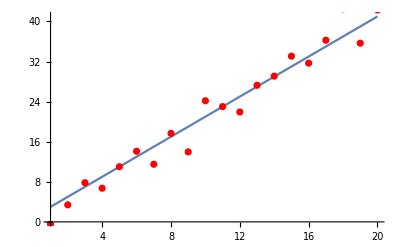

```mathematica
σ=3;α=1;β=2;
n=20;
X=Range[n];
Y=α+β*X+RandomVariate[NormalDistribution[0,σ],n];
p=Show[Plot[α+β*x,{x,Min[X],Max[X]}],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
```

```mathematica
stanData=<|"N"->n,"x"->X,"y"->Y|>;
stanDataFile=ExportStanData[stanExeFile,stanData]
```

ExportStanData[CompileStanCode[stanCodeFile,StanVerbose→False],<|N→20,x→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},y→{-0.479584,3.40388,7.82051,6.72129,11.0087,14.1001,11.5059,17.6665,13.9743,24.1776,23.0119,21.9347,27.2656,29.0886,33.0806,31.6883,36.2562,42.5198,35.6707,42.303}|>]

## Option modification example

A run with sample default options

```mathematica
stanResultFile=RunStan[stanExeFile,SampleDefaultOptions]
```

RunStan[CompileStanCode[stanCodeFile,StanVerbose→False],method=sample ]

Now with customized option values

Note: 

you can see available options looking at previous command output or by reading CmdStan manual
https://mc-stan.org/docs/2_24/cmdstan-guide-2_24.pdf

by example we will modify MCMC options:
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default) 
    
  and
  
   algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)

#### Copy default Sample option

```mathematica
myOpt=SampleDefaultOptions
```

method=sample

#### Modify some values

```mathematica
myOpt=SetStanOption[myOpt,"adapt.num_samples",2000]
myOpt=SetStanOption[myOpt,"adapt.num_warmup",1500]
myOpt=SetStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth",5]
```

method=sample adapt num_samples=2000

method=sample adapt num_samples=2000 num_warmup=1500

method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5

#### Perform a new run with these options

```mathematica
stanResultFile=RunStan[stanExeFile,myOpt]
```

RunStan[CompileStanCode[stanCodeFile,StanVerbose→False],method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5 ]

### Read back option values

```mathematica
GetStanOption[myOpt,"adapt.num_warmup"]
GetStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth"]
```

1500

5

### Remove the preivously customized “max_depth” value

```mathematica
myOpt=RemoveStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth"]
```

method=sample adapt num_samples=2000 num_warmup=1500